# Collision Events in Dynamic Systems

## Bouncing ball

{{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],xdot[t]→InterpolatingFunction[…][t],ydot[t]→InterpolatingFunction[…][t]}},{{5.58258,13.0063,19.0196,23.8903,27.8356,31.0313,33.6198,35.7165}}}

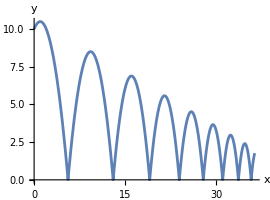

{{5.58258,13.0063,19.0196,23.8903,27.8356,31.0313,33.6198,35.7165}}

```mathematica
Reap[NDSolve[{
x'[t]==xdot[t],
y'[t]==ydot[t],
xdot'[t]==0,
ydot'[t]==-1,
x[0]==0,
y[0]==10,
xdot[0]==1,
ydot[0]==1,
WhenEvent[y[t]==0,{
ydot[t]->-0.9ydot[t],
xdot[t]->0.9xdot[t],
Sow[x[t]]
}
]
},{x[t],y[t],xdot[t],ydot[t]},
{t,0,50}]]
ParametricPlot[{x[t],y[t]}/.%[[1]],{t,0,50},AxesLabel->{"x","y"}]
%%[[2]]
```

### Second Order Equations

{{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}},{{5.58258,13.0063,19.0196,23.8903,27.8356,31.0313,33.6198,35.7165}}}

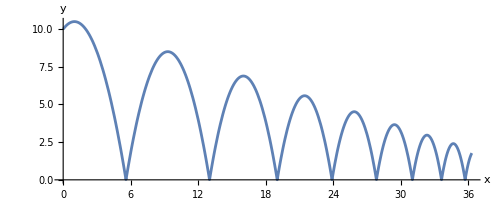

```mathematica
Reap[NDSolve[{
x''[t]==0,
y''[t]==-1,
x[0]==0,
y[0]==10,
x'[0]==1,
y'[0]==1,
WhenEvent[y[t]==0,{
y'[t]->-0.9y'[t],
x'[t]->0.9x'[t],
Sow[x[t]]
}
]
},{x[t],y[t]},
{t,0,50}]]
ParametricPlot[{x[t],y[t]}/.%[[1]],{t,0,50},AxesLabel->{"x","y"}]
```

## Double Pendulum - Poincaré Maps

For a fixed energy, given three coordinates, the fourth is restricted to a finite number of discrete choices. So we can plot orbits in 3D without losing generality.
Poincaré maps take this further and plot where the 3d orbits intersect with a defined plane, to go from continuous curves to discrete points on the orbit.
In this case, we are plotting θ, θdot, φdot, from there φ is determined. We then plot the values of θdot and φdot as θ-φ = 0.

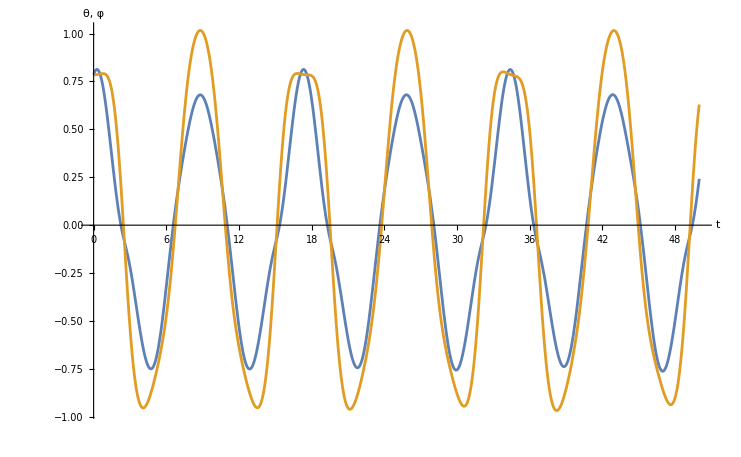

-Graphics3D-

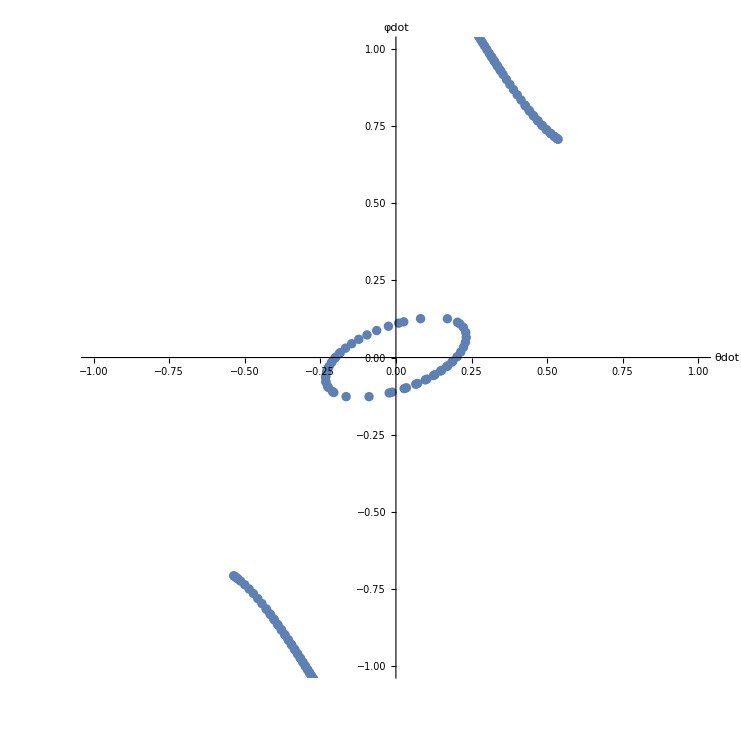

```mathematica
Reap@NDSolve[{
θ'[t]==θdot[t],
φ'[t]==φdot[t],
θdot'[t]==1/(2-Cos[θ[t]-φ[t]]^2)(-2 Sin[θ[t]]+Cos[θ[t]-φ[t]] Sin[φ[t]]-Cos[θ[t]-φ[t]] Sin[θ[t]-φ[t]] θdot[t]^2-Sin[θ[t]-φ[t]] φdot[t]^2),
φdot'[t]==1/(2-Cos[θ[t]-φ[t]]^2)(2 Cos[θ[t]-φ[t]] Sin[θ[t]]-2 Sin[φ[t]]+2 Sin[θ[t]-φ[t]] θdot[t]^2+Cos[θ[t]-φ[t]] Sin[θ[t]-φ[t]] φdot[t]^2),
θ[0]==π/4,
φ[0]==π/4,
θdot[0]==0.2,
φdot[0]==0,
WhenEvent[Mod[θ[t]-φ[t],2π]==0,{Sow[{θ[t],φ[t],θdot[t],φdot[t]}]}]
},{θ[t],φ[t],θdot[t],φdot[t]},
{t,0,500}];
Plot[Evaluate[{θ[t],φ[t]}/.%[[1]]],{t,0,50},AxesLabel->{"t","θ, φ"}]
ParametricPlot3D[{θdot[t],φdot[t],Mod[θ[t]-φ[t]+π,2π]-π}/.%%[[1]],{t,0,500},PlotStyle->Thin,AxesLabel->{"θdot","φdot","θ-φ"}]
ListPlot[Map[{#[[3]],#[[4]]}&,%%%[[2,1]]],AxesLabel->{"θdot","φdot"},AspectRatio->1,PlotRange->{{-1,1},{-1,1}}]
```

### More Poincaré map examples

In this section, we’ll draw more Poincaré maps with varying initial conditions. You’ll see that chaotic orbits can suddenly onset as the energy is increased.
Do note these figures can take a while to run.

```mathematica
energy={θ,φ,θdot,φdot}↦3+1/2(2 θdot^2+φdot^2+2θdot φdot Cos[θ-φ])-2 Cos[θ]-Cos[φ];
equationsOfMotion={
θ'[t]==θdot[t],
φ'[t]==φdot[t],
θdot'[t]==1/(2-Cos[θ[t]-φ[t]]^2)(-2 Sin[θ[t]]+Cos[θ[t]-φ[t]] Sin[φ[t]]-Cos[θ[t]-φ[t]] Sin[θ[t]-φ[t]] θdot[t]^2-Sin[θ[t]-φ[t]] φdot[t]^2),
φdot'[t]==1/(2-Cos[θ[t]-φ[t]]^2)(2 Cos[θ[t]-φ[t]] Sin[θ[t]]-2 Sin[φ[t]]+2 Sin[θ[t]-φ[t]] θdot[t]^2+Cos[θ[t]-φ[t]] Sin[θ[t]-φ[t]] φdot[t]^2)
};
```

```mathematica
initialConditions={
θ[0]==0.42π,
φ[0]==0.42 π,
θdot[0]==0,
φdot[0]==0
};
Reap@NDSolve[{
Sequence@@equationsOfMotion,
Sequence@@initialConditions,
WhenEvent[Mod[θ[t]-φ[t],2π]==0,{Sow[{θ[t],φ[t],θdot[t],φdot[t]}]}]
},{θ[t],φ[t],θdot[t],φdot[t]},
{t,0,500000}];
ListPlot[Map[{#[[3]],#[[4]]}&,%[[2,1]]],PlotRange->{{-3.3,3.3},{-3.3,3.3}},AspectRatio->1,AxesLabel->{"θdot","φdot"}]
```

-Graphics-

Changing the energy here alters the shape of the orbit, Opening out the central feature.

```mathematica
initialConditions={
θ[0]==0.435π,
φ[0]==0.435 π,
θdot[0]==0,
φdot[0]==0
};
Reap@NDSolve[{
Sequence@@equationsOfMotion,
Sequence@@initialConditions,
WhenEvent[Mod[θ[t]-φ[t],2π]==0,{Sow[{θ[t],φ[t],θdot[t],φdot[t]}]}]
},{θ[t],φ[t],θdot[t],φdot[t]},
{t,0,500000}];
ListPlot[Map[{#[[3]],#[[4]]}&,%[[2,1]]],PlotRange->{{-3.3,3.3},{-3.3,3.3}},AspectRatio->1,AxesLabel->{"θdot","φdot"}]
```

-Graphics-

```mathematica
initialConditions={
θ[0]==0.4396π,
φ[0]==0.4396 π,
θdot[0]==0,
φdot[0]==0
};
Reap@NDSolve[{
Sequence@@equationsOfMotion,
Sequence@@initialConditions,
WhenEvent[Mod[θ[t]-φ[t],2π]==0,{Sow[{θ[t],φ[t],θdot[t],φdot[t]}]}]
},{θ[t],φ[t],θdot[t],φdot[t]},
{t,0,500000}];
ListPlot[Map[{#[[3]],#[[4]]}&,%[[2,1]]],PlotRange->{{-3.3,3.3},{-3.3,3.3}},AspectRatio->1,AxesLabel->{"θdot","φdot"}]
```

-Graphics-

This next map is only slightly higher energy than the last, but shows completely different dynamics.

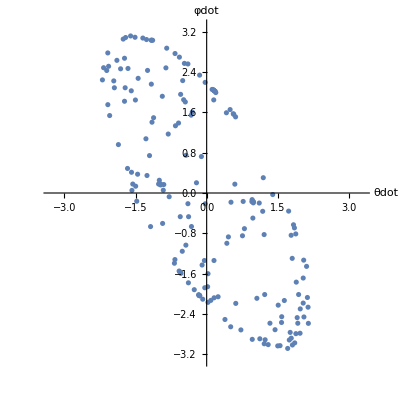

```mathematica
initialConditions={
θ[0]==0.4397π,
φ[0]==0.4397 π,
θdot[0]==0,
φdot[0]==0
};
Reap@NDSolve[{
Sequence@@equationsOfMotion,
Sequence@@initialConditions,
WhenEvent[Mod[θ[t]-φ[t],2π]==0,{Sow[{θ[t],φ[t],θdot[t],φdot[t]}]}]
},{θ[t],φ[t],θdot[t],φdot[t]},
{t,0,500000}];
ListPlot[Map[{#[[3]],#[[4]]}&,%[[2,1]]],PlotRange->{{-3.3,3.3},{-3.3,3.3}},AspectRatio->1,AxesLabel->{"θdot","φdot"}]
```

### Bifurcation maps

For these next figures, we’ll compress the Poincaré maps from earlier, that are plotting θdot and φdot into just showing the φdot axis, but varying energy.
Again, see the sudden onset of chaos. Note for different starting conditions, there are solution spaces with different onsets.
This first figure starts with θ = φ at rest.
These figures take an even longer time to run!

```mathematica
Table[Module[{
initialConditions={θ[0]==ArcCos[(3-ee)/3],φ[0]==ArcCos[(3-ee)/3],θdot[0]==0,φdot[0]==0}
},Reap[NDSolve[{
Sequence@@equationsOfMotion,
Sequence@@initialConditions,
WhenEvent[Mod[θ[t]-φ[t],2π]==0,{Sow[φdot[t]]}]
},{θ[t],φ[t],θdot[t],φdot[t]},
{t,0,5000}]][[2,1]]//Map[{ee,#}&]
],{ee,0.005,6,0.01}]//(Flatten[#,1]&);
%//(ListPlot[#,PlotRange->Full,PlotStyle->{Opacity[0.05],PointSize[Tiny]},AxesLabel->{"E","φdot"}]&)
```

-Graphics-

This figure starts with θ = -φ at rest.

```mathematica
Table[Module[{
initialConditions={θ[0]==ArcCos[(3-ee)/3],φ[0]==-ArcCos[(3-ee)/3],θdot[0]==0,φdot[0]==0}
},Reap[NDSolve[{
Sequence@@equationsOfMotion,
Sequence@@initialConditions,
WhenEvent[Mod[θ[t]-φ[t],2π]==0,{Sow[φdot[t]]}]
},{θ[t],φ[t],θdot[t],φdot[t]},
{t,0,5000}]][[2,1]]//Map[{ee,#}&]
],{ee,0.005,6,0.01}]//(Flatten[#,1]&);
%//(ListPlot[#,PlotRange->Full,PlotStyle->{Opacity[0.05],PointSize[Tiny]},AxesLabel->{"E","φdot"}]&)
```

This figure starts with θ = φ = θdot = 0 with an increasing φdot.

```mathematica
Table[Module[{
initialConditions={θ[0]==0,φ[0]==0,θdot[0]==0,φdot[0]==√(2ee)}
},Reap[NDSolve[{
Sequence@@equationsOfMotion,
Sequence@@initialConditions,
WhenEvent[Mod[θ[t]-φ[t],2π]==0,{Sow[φdot[t]]}]
},{θ[t],φ[t],θdot[t],φdot[t]},
{t,0,5000}]][[2,1]]//Map[{ee,#}&]
],{ee,0.005,6,0.01}]//(Flatten[#,1]&);
%//(ListPlot[#,PlotRange->Full,PlotStyle->{Opacity[0.05],PointSize[Tiny]},AxesLabel->{"E","φdot"}]&)
```

This figure starts with θ = φ = φdot = 0 with an increasing θdot .

```mathematica
Table[Module[{
initialConditions={θ[0]==0,φ[0]==0,θdot[0]==√ee,φdot[0]==0}
},Reap[NDSolve[{
Sequence@@equationsOfMotion,
Sequence@@initialConditions,
WhenEvent[Mod[θ[t]-φ[t],2π]==0,{Sow[φdot[t]]}]
},{θ[t],φ[t],θdot[t],φdot[t]},
{t,0,5000}]][[2,1]]//Map[{ee,#}&]
],{ee,0.005,6,0.01}]//(Flatten[#,1]&);
%//(ListPlot[#,PlotRange->Full,PlotStyle->{Opacity[0.05],PointSize[Tiny]},AxesLabel->{"E","φdot"}]&)
```